# CCBH-Power Law + Peak: ParameterDependenceTest

Davi  C. Rodrigues (this code). July, 2023.

```mathematica
ResourceFunction["DarkMode"][]
```

CCBH = Cosmologically coupled black hole (general case)
DEBH = Dark energy coupled Black Hole (implies k = - 3w)
GBH = Growing BH, k is arbitrary and without direct dark energy impact.
m1 = primary (larger) mass of the BBH or NSBH pair.

Naming conventions:
All defined variables/functions start with lower case letter.
“I” at the end of a function name: interpolated version. 
“Raw”: a function without options. It is useful to store results. The version with options is based on the raw version.

## Starting...

```mathematica
SetDirectory[NotebookDirectory[]];
Get[FileNameJoin[{"codes", "Directories.wl"}]];

(*
  Calling wl files
  ***************** 
*)

getCode["Constants.wl"];
baseSimPoints = 5 10^5; (*The base number of points to be simmulated for each dimension, commonly 10^5-10^7, depends on the purpose.*)

getCode["PowerLawPlusPeakDefinition.wl"];
getCode["Cosmology.wl"];

Print["End of running wl files."];

(*
  GENERAL PURPOSE FUNCTIONS
  **************************
*)

findSigma::usage = "findSigma[probability] yields the number of σ's for a given probability.";
findSigma[prob_] := Block[{sigma}, 
  sigma /. FindRoot[NProbability[RealAbs[x] > sigma , x\[Distributed]NormalDistribution[]] == prob, {sigma, 2}]
];

Clear[outSigma];
outSigma[n_] := outSigma[n] = NProbability[RealAbs[x] > n, x\[Distributed]NormalDistribution[]];
```

Starting Constants.wl:

Starting PowerLawPlusPeakDefinition.wl:

Use plpp`pi[m, options] for the power-law-plus-peak PDF and plpp`𝒟[options] for the distribution. Use optionsPlpp to see the options.

Starting Cosmology.wl:

tableZformation loaded.

End of running wl files.

## Testing PLPP parameter dependence (using 3 10^5)

here I have to select randomly different PLPP values and find the probability with reference values.

```mathematica
(*The quantiles for GWTC-3 PLPP parameters, 5%, 16%, Median, 84%, 95%. Provided by Sumit Kumar.*)

(*
alpha = Around[#3, {#1 - #3, #5-#3 }] & @@ Evaluate@ReleaseHold[Hold[2.91368096 3.10533638 3.40401232 3.73461844 3.98690423] /. Times -> List];
beta =  Around[#3, {#1 - #3, #5-#3 }]& @@ ReleaseHold[Hold[-0.24646612  0.23829546  1.07679192  2.04662647  2.83787879] /. Times -> List ] ;
mmax = Around[#3, {#1 - #3, #5-#3 }]& @@ ReleaseHold[Hold[77.49731724 79.92731197 86.85433456 94.93299396 98.2530281] /. Times -> List ];
mmin = Around[#3, {#1 - #3, #5-#3 }]& @@ ReleaseHold[Hold[3.55443173 4.21290074 5.08383396 5.68043848 5.95357982] /. Times -> List ];
lam = Around[#3, {#1 - #3, #5-#3 }]& @@ ReleaseHold[Hold[0.01308824 0.02074258 0.03868563 0.06805879 0.09687909] /. Times -> List ];
mpp = Around[#3, {#1 - #3, #5-#3 }]& @@ ReleaseHold[Hold[29.93629207 31.68191701 33.72549972 35.13203767 35.98450818] /. Times -> List ];
sigpp = Around[#3, {#1 - #3, #5-#3 }]& @@ ReleaseHold[Hold[1.45384514 2.07879345 3.55853002 6.07252803 8.14412684] /. Times -> List ];
deltam = Around[#3, {#1 - #3, #5-#3 }]& @@ ReleaseHold[Hold[1.60127061 2.97112556 4.82841 6.8000636  8.15460135] /. Times -> List ];
*)

(*
  minA[around_] := around /. Around[x_, y_] :>  x - y[[1]];
  maxA[around_] := around /. Around[x_, y_] :>  x + y[[2]];
  randomPP[parameter_] := RandomVariate[UniformDistribution[{minA[parameter], maxA[parameter]}]];
*)

assoSamplesPLPPraw = Import[FileNameJoin[{pathIn, "all_samples_PLPP_GWTC3.h5"}], "Data"]; (*Data imported as association, asso for short.*)
assoSamplesPLPP = KeyMap[StringDelete[#, {"/", "_"}] & , assoSamplesPLPPraw]; (*Removes inconvenient strings from the key names.*) 

alpha = assoSamplesPLPP["alpha"];
beta = assoSamplesPLPP["beta"];
mmax = assoSamplesPLPP["mmax"];
mmin = assoSamplesPLPP["mmin"];
lam = assoSamplesPLPP["lam"];
mpp = assoSamplesPLPP["mpp"];
sigpp = assoSamplesPLPP["sigpp"];
deltam = assoSamplesPLPP["deltam"];

lengthSample = Length @ alpha;
```

Modified version of the MassFactorCorrection.wl code, to allow for parameter variation: no memory.

```mathematica
ClearAll[
  massFactorDelay, 
  dataMassFactor,
  dataDelayTime,
  minDelayTime, 
  maxDelayTime
];

Echo[baseSimPoints, "Base number of simmulated points per dimension (baseSimPoints): "];

listDelayTime = Range[tdmin0/10, tdmax0, 0.015]; (* delayTime values to be computed. tdmin lower than tdmin0 will be considered*)
listzObs = Range[0.0, 1.0, 0.01];
listw = Range[-1.5, -0.5, 0.1]; 

minDelayTime = First[listDelayTime]; (*min delay time to be computed, it can be lower than tdmin0*)
maxDelayTime[zObs_, tdmax_?NumberQ, zMax_?NumberQ, w_] :=  Min[
  tdmax,
  timeZ[zObs, zMax, w]
]; 

massFactor[zObs_,zFormation_, k_] = ((1 + zFormation)/(1 + zObs))^k; (*(a/a_i)^k. This is the factor that corrects the mass*)

SetAttributes[massFactorDelay, Listable];
massFactorDelay[zObs_, delayTime_, k_, zMax_, w_] =  massFactor[zObs, zFormationI[zObs, delayTime, zMax, w], k];

randomLogDelayTime[zObs_, tdmin_, tdmax_, zMax_, w_, realizations_] := 
 RandomReal[{Log10[tdmin], Log10 @ maxDelayTime[zObs, tdmax, zMax, w]}, realizations]; (*log-flat distribution.*)

dataDelayTime[zObs_, tdmin_, tdmax_, zMax_, w_] := 
 10^randomLogDelayTime[zObs, tdmin, tdmax, zMax, w,  proportionalBaseSimPoints[tdmin, tdmax]]; 

dataMassFactor[zObs_, tdmin_, tdmax_, k_, zMax_, w_] := 
 massFactorDelay[zObs, dataDelayTime[zObs, tdmin, tdmax, zMax, w], k, zMax, w];
 
(*
  FORMATION MASS
  ***********
*)

(* ::Section:: *)
(* Formation Mass *)

Clear[dataM1FormationRaw, dataM1Formation, dataM1Merger];

Clear[𝒟plp];
tabRandom = {};
𝒟plp := (
  random = RandomInteger[lengthSample];
  AppendTo[tabRandom, random];
  plpp`dist[
    plpp`a -> alpha[[random]],
    plpp`mMin -> mmin[[random]],
    plpp`dm -> deltam[[random]],
    plpp`mMax -> mmax[[random]],
    plpp`mu -> mpp[[random]],
    plpp`s -> sigpp[[random]],
    plpp`l -> lam[[random]],
    plpp`betaQ -> beta[[random]]
  ]
); (*plpp`𝒟 is defined in PowerLawPlusPeakDefinition.wl.*)

dataM1Merger := RandomVariate[𝒟plp, baseSimPoints];  (*2 baseSimPoints is not necessary here*)

dataM1FormationRaw[zObs_, tdmin_, tdmax_, k_, zMax_, w_]:= Block[
  {length, dataM1MergerSameLength},
  length = Length @ dataMassFactor[zObs, tdmin, tdmax, k, zMax, w];
  dataM1MergerSameLength = Take[dataM1Merger, length];
  1/dataMassFactor[zObs, tdmin, tdmax, 1, zMax, w]^k dataM1MergerSameLength 
];

dataM1Formation[zObs_, opts:OptionsPattern[optionstkw]] := dataM1FormationRaw[
  zObs, 
  OptionValue @ tdmin, 
  OptionValue @ tdmax, 
  OptionValue @ k, 
  OptionValue @ zMax, 
  OptionValue @ w
];

𝒟M1FormationEmpRaw[zObs_, tdmin_, tdmax_, k_, zMax_, w_] := 
 EmpiricalDistribution[
   dataM1FormationRaw[zObs, tdmin, tdmax, k, zMax, w]
 ];

𝒟M1FormationEmp[zObs_, opts:OptionsPattern[optionstkw]] := 𝒟M1FormationEmpRaw[
  zObs, 
  OptionValue @ tdmin, 
  OptionValue @ tdmax, 
  OptionValue @ k, 
  OptionValue @ zMax, 
  OptionValue @ w
];

probabilityMminApprox[mMin_, opts:OptionsPattern[optionstkw]] := SurvivalFunction[𝒟M1FormationEmp[0.4, opts], mMin]^72;
probabilityMminDoubleApprox[mMin_, opts:OptionsPattern[optionstkw]] := SurvivalFunction[𝒟M1FormationEmp[0.4, opts], mMin]^(2*72);
```

Base number of simmulated points per dimension (baseSimPoints):   500000

```mathematica
isComputeTension3 = True; (*Takes 4 hours for 10^3 probabilities, saved with baseSimPoints = 5 10^5*) 

If[isComputeTension3, 
  Echo["Computing the tension..."];
  listProbSamplePLPP3 = Monitor[Table[findSigma[probabilityMminApprox[2]], {i, 1000}], i]; // EchoTiming;
  dumpsave["listProbSamplePLPP3.mx", listProbSamplePLPP3];
  dumpsave["tabRandomPLPP3.mx", tabRandom],
  (*else*)
  getAux["listProbSamplePLPP3.mx"];
  Echo["listProbSamplePLPP3.mx loaded."];
];
```

Computing the tension...

17763.7

The number of repeated realizations:

```mathematica
Length@tabRandom  - Length@FindRepeat[tabRandom]
```

0

The smaller tension values and their corresponding random values:

```mathematica
SortBy[{tabRandom, listProbSamplePLPP3}ᵀ, Last][[1;;10]]
```

{{6850,2.72742},{5999,2.74446},{3624,2.75677},{4477,2.76559},{1218,2.83535},{6068,2.85029},{10227,2.85688},{6701,2.87967},{11122,2.88405},{2675,2.88469}}

Median:   3.69213

5% quantile:   3.18297

95% quantile:   3.94911

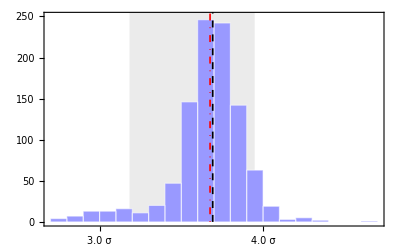

pathOut/histSamplePLPP3.pdf

```mathematica
histSamplePLPP3 = Histogram[
  listProbSamplePLPP3, 
  {0.1}, 
  Axes -> False, 
  Frame -> True , 
  Background->White, 
  ChartBaseStyle->EdgeForm[White], 
  ChartStyle->Directive[Opacity[1], Lighter[Blue, 0.6]], 
  FrameStyle-> Directive[Black, FontSize -> 13], 
  FrameTicksStyle-> Directive[Black, FontFamily-> "Times"],
  FrameTicks-> {{Automatic, Automatic}, {Table[{i, ToString@NumberForm[i, {2,1}]<>ToString@Style[" σ", FontFamily-> "Times"]}, {i, 1, 5, 0.2}], Automatic}},
  Epilog-> {Dashed, Black, Thickness[0.003], Line[{{Median @ listProbSamplePLPP3, 0}, {Median @ listProbSamplePLPP3, 1000}}], Red, DotDashed, Line[{{3.676, 0}, {3.676, 1000}}]}
];

Median @ listProbSamplePLPP3 ~ Echo ~ "Median: ";
quantMin90 = Quantile[listProbSamplePLPP3, 0.05] ~ Echo ~ "5% quantile: ";
quantMax90 = Quantile[listProbSamplePLPP3, 0.95] ~ Echo ~ "95% quantile: ";

plot90 = Plot[500, {x, quantMin90, quantMax90}, Filling->Automatic, FillingStyle->{Directive[LightGray, Opacity[0.5]]}, 
  Axes -> False, 
  Frame -> True , 
  Background->White, 
  FrameStyle-> Directive[Black, FontSize -> 13], 
  FrameTicksStyle-> Directive[Black, FontFamily-> "Times"],
  FrameTicks-> {{Automatic, Automatic}, {Table[{i, ToString@NumberForm[i, {2,1}]<>ToString@Style[" σ", FontFamily-> "Times"]}, {i, 1, 5, 0.5}], Automatic}},
  PlotRangePadding->None
];

histSamplePLPP3 = Show[plot90, histSamplePLPP2, PlotRange-> {All, {0,250}}, Epilog-> {Dashed, Black, Thickness[0.003], Line[{{Median @ listProbSamplePLPP3, 0}, {Median @ listProbSamplePLPP3, 1000}}], Red, DotDashed, Line[{{3.676, 0}, {3.676, 1000}}]}]

exportOut["histSamplePLPP3.pdf", histSamplePLPP3]
```